All Things Chebyshev

Elliott Freeman & Cole Pendergraft

To begin any discussion of all things Chebyshev, we first must take a look at the Chebyshev polynomials and understand what they provide us in terms of polynomial interpolation and approximation. We can define the Chebyshev polynomials as “a sequence of orthogonal polynomials that are related to De Moivre’s formula.” De Moivre’s formula, put very simply, is a tool for computing powers of complex numbers. So how in the world is a tool used to compute powers of complex numbers going to help us in polynomial interpolation? To answer this question, we need to look at the properties of a Chebyshev polynomial, and to do that we need to have some understanding about how they are created, and what they are in a mathematical sense.

There are various forms of the Chebyshev polynomials, but for our purpose we are looking particularly at the  n^th Chebyshev Polynomial of the first kind. We define this polynomial, denoted as T_n(x), as follows:

(1) T_n(x) = cos(n cos^-1(x))

which can be re-written into the form:

(2) T_n(cos(θ)) = cos nθ

We find that this second form is more useful for creating our polynomials, as we have well established relationships for cos nθ elements:

cos 0θ = 1
	cos 1θ = cos θ
	cos 2θ = 2 cos^2 θ - 1
	cos 3θ = 4 cos^3 θ - 3cos θ

Substituting this relationship into our generating function for Chebyshev polynomials of the first kind, and substituting x = cos θ, we find that we can generate the first four Chebyshev polynomials with relative ease:

T_0(x) = 1
	T_1(x) = x
	T_2(x) = 2 x^2 - 1
	T_3(x) = 4 x^3 - 3x

We could keep progressing in this way, creating relationships in terms of cos θ, but that is going to rapidly get very complex, as we can see by taking a look at cos 4θ:

cos 4θ = cos(θ)cos(3θ) - sin(θ)sin(3θ)

Note that the addition of the two sin θ elements is going to complicate our formula, as we want polynomials in terms of cos θ. It’s not impossible, however, to continue progressing with this method, as we know that

sin 3θ = 3sin θ - 4 sin^3 θ

which makes our equation for cos 4 θ

cos 4θ = cos θ cos 3θ - sin θ sin 3θ = cos θ (4 cos^3 θ - 3cos θ) - 3 sin^2 θ - 4 sin^4 θ
	⟹ 4 cos^4θ - 3 cos^2θ + 3(1 - cos^2θ) - 4(1 - cos^2θ)^2
	⟹ 8 cos^4θ - 8 cos^2θ + 1
	
	and thus,
	
	T_4(x) = 8 x^4 - 8 x^2 + 1

If we really enjoy tedious math we could continue on with this strategy, breaking down all of our sin terms and writing them in terms of cos, but higher and higher degrees are going to end up having more and more sin terms attached to it, leaving us in nested expression hell. This demonstrates our need for a more simple relationship that we can use to reliably generate these successive polynomials, by hand or otherwise. We can accomplish this task by making use of a fact that stems from trigonometric sum and product rules:

cos(n + 1)θ + cos(n - 1)θ = 2cosθ cos nθ

which manipulates to

cos(n + 1)θ = 2cosθ cos nθ -  cos(n - 1)θ

Given that T_n(cos θ) = cos nθ, and thusly that T_(n-1)(cos θ) = cos(n - 1)θ and T_(n + 1)(cos θ) = cos(n + 1)θ, we are now able to establish a recursive relationship for the Chebyshev polynomials:

(3) T_(n + 1)(x) = 2xT_n(x) - T_(n - 1)(x)

Utilizing this and our knowledge that T_0(x) = 1 and T_1(x) = x, we are now able to establish all of the successive Chebyshev polynomials by hand ad infinitum.

The nice thing about using a computer, however, is that we don’t need to worry about all this complex hand-written math, and can instead just pass our known relationships into a for loop in order to generate as many polynomials as we would like.

```mathematica
clear[f, g];
f[n_, θ_] = Cos[θ * n];
g[n_, θ_] = 2Cos[θ]* f[n-1, θ] - f[n-2, θ]; (* Equation (3) above re-indexed such that n + 1 = n, n = n - 1, and n - 1 = n - 2 *)

Print["Degree 0 Chebyshev polynomial is T[Cos[θ]] = 1"]
Print["Degree 1 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]"]
For[i = 2, i <= 10, i++, Print["Degree ", i, " Chebyshev polynomial is T[Cos[θ]] = ", TrigExpand[g[i, θ]]]]{
}
(* The polynomials that are output from this for loop will have a slightly different form from those demonstrated in the initial discussion of Chebyshev polynomials, and this is due to how Mathematica reduces and expands trigonometric funtions. They are indeed the same equations, just not reduced to quite the same extent. *)
```

Degree 0 Chebyshev polynomial is T[Cos[θ]] = 1

Degree 1 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]

Degree 2 Chebyshev polynomial is T[Cos[θ]] = -1+2 Cos[θ]^2

Degree 3 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^3-3 Cos[θ] Sin[θ]^2

Degree 4 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4

Degree 5 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^5-10 Cos[θ]^3 Sin[θ]^2+5 Cos[θ] Sin[θ]^4

Degree 6 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^6-15 Cos[θ]^4 Sin[θ]^2+15 Cos[θ]^2 Sin[θ]^4-Sin[θ]^6

Degree 7 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^7-21 Cos[θ]^5 Sin[θ]^2+35 Cos[θ]^3 Sin[θ]^4-7 Cos[θ] Sin[θ]^6

Degree 8 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^8-28 Cos[θ]^6 Sin[θ]^2+70 Cos[θ]^4 Sin[θ]^4-28 Cos[θ]^2 Sin[θ]^6+Sin[θ]^8

Degree 9 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^9-36 Cos[θ]^7 Sin[θ]^2+126 Cos[θ]^5 Sin[θ]^4-84 Cos[θ]^3 Sin[θ]^6+9 Cos[θ] Sin[θ]^8

Degree 10 Chebyshev polynomial is T[Cos[θ]] = Cos[θ]^10-45 Cos[θ]^8 Sin[θ]^2+210 Cos[θ]^6 Sin[θ]^4-210 Cos[θ]^4 Sin[θ]^6+45 Cos[θ]^2 Sin[θ]^8-Sin[θ]^10

{}

Just as a sanity check, lets compare some outputs from our code generated functions to the known outputs from Chebyshev polynomials:

```mathematica
t[θ_] = 512 Cos[θ]^10 - 1280 Cos[θ]^8 + 1120 Cos[θ]^6 - 400 Cos[θ]^4 + 50 Cos[θ]^2 - 1; (* Equation above is the degree 10 Chebyshev polynomial with all instances of Sinθ adjusted to be Cosθ. It is typically written with Cosθ = x to simplify reading, but I have substituted Cosθ back in for x to maintain symmetry between this equation and our generated equation *)

q[θ_] = Cos[θ]^10-45 Cos[θ]^8 Sin[θ]^2+210 Cos[θ]^6 Sin[θ]^4-210 Cos[θ]^4 Sin[θ]^6+45 Cos[θ]^2 Sin[θ]^8-Sin[θ]^10; (* Our degree 10 polynomial *)

(* Lets compare a few simple examples just to make absolutely sure our generated equations match the known equations *)
t[1.]
q[1.]

t[2.]
q[2.]

t[3.]
q[3.]
```

-0.839072

-0.839072

0.408082

0.408082

0.154251

0.154251

So now we see that the format differences simply come down to Mathematica not wanting to spend a whole bunch of time constructing these equations in terms of a single trig function, and honestly, you can’t blame it. Despite the format differences, we can be assured that we will be working with the same polynomials. For the interested reader, below I have included the 0^th to 10^th degree polynomials in their simplest form (remember, x = cos θ):

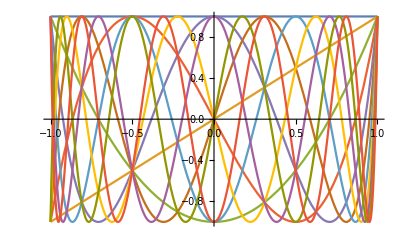

```mathematica
T0[x_] = 1;
T1[x_] = x;
T2[x_] = 2 x^2 - 1;
T3[x_] = 4 x^3 - 3x;
T4[x_] = 8 x^4 - 8 x^2 + 1;
T5[x_] = 16 x^5 - 20 x^3 + 5x;
T6[x_] = 32 x^6 - 48 x^4 + 18 x^2 - 1;
T7[x_] = 64 x^7 - 112 x^5 + 56 x^3 - 7x;
T8[x_] = 128 x^8 - 256 x^6 + 160 x^4 - 32 x^2 + 1;
T9[x_] = 256 x^9 - 576 x^7 + 432 x^5 - 120 x^3 + 9x;
T10[x_] = 512 x^10 - 1280 x^8 + 1120 x^6 - 400 x^4 + 50 x^2 - 1;
Plot[{T0[x], T1[x], T2[x], T3[x], T4[x], T5[x], T6[x], T7[x], T8[x], T9[x], T10[x]}, {x, -1, 1}]
```

Great! So now we have a pretty graph, a bunch of functions related to finding powers of complex numbers, and the tools to make more! So what does this have to do with interpolation? The answer to your question will arrive shortly!

The part of Chebyshev polynomials that starts becoming applicable to approximation comes when you begin to take roots of these equations. That said, for our analysis purposes we don’t want to achieve numerical roots, we want roots in their most generalized form, and Mathematica does not like creating generalized formulas, it wants to output a discrete quantity, so this is a root we need to take by hand. Fortunately, that isn’t too bad of a process.

Let’s attempt to find the roots of T_n(x) = 0:

	Step 1: Substitute in x = cosθ, so now we are finding the roots of

T_n(cosθ) = cos nθ = 0

Step 2: The roots of this equation occur where nθ = π/2 + kπ for some k in ℤ. Thus,

θ = π/(2n) + kπ/n = (((2k + 1)π)/(2n))

Step 3: With this equality, we now have

x = cosθ = cos(((2k + 1)π)/(2n))
		
		and we are done!

Now is when things start to get interesting. We can denote the roots of our equation with respect to k as:

	x_k = cos(((2k + 1)π)/(2n)),  k = 1, 2, ..., n
	
	where n is the degree of the polynomial you are seeking.

These particular roots are known as Chebyshev nodes, and they have vast applications in the world of approximation and interpolation. It is very important to note that this particular form works only if using the interval [-1, 1]. If we want instead to find nodes over an arbitrary interval [a ,b] we have to use what is called an affine transformation to generate our node equation, which is as follows:

x_k = 1/2(a + b) + 1/2(b - a)cos(((2k -1)π)/(2n)),  k = 1, ... ,n

If [-1, 1] is entered into this equation, it will just return our original equation, so what we have here is the perfectly generalized form of the roots of Chebyshev polynomials. We see that this is the power of Chebyshev polynomials in relation to interpolation and approximation, they provide us the function that we can use to create Chebyshev nodes, which is what we will be talking about for the remainder of this discussion.

In order to understand Chebyshev nodes, you have to understand a situation known as Runge’s Phenomenon. Take for example, the polynomial approximation of the following function on the interval [-1,1].

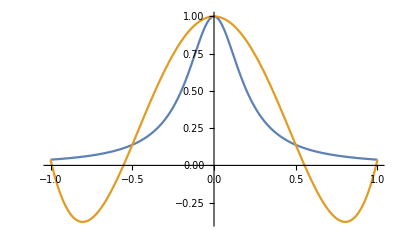

```mathematica
Clear[f,points,approx,error];
f[x_] = 1/(1+25x^2);
points =Table[{i,f[i]},{i,-1,1,0.5}];
approx[x_] = InterpolatingPolynomial[points,x];
Plot[{f[x],approx[x]},{x,-1,1}]
```

Using Theorem 4.2.2 page 158 from Cheney and Kincaid’s Numerical Mathematics and Computing Sixth Edition we can estimate the maximum error. The first step is to find the fifth derivative of the function. Next we find what our fifth derivative of the function is bounded by. Then we can plug that into our theorem to find the maximum error.

-(37500000000 x^5)/((1+25 x^2)^6)+(1500000000 x^3)/((1+25 x^2)^5)-(11250000 x)/((1+25 x^2)^4)

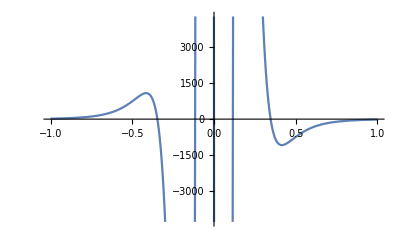

{313934.,{x→-0.0456487}}

{-313934.,{x→0.0456487}}

```mathematica
deriv = D[f[x],{x,5}]
Plot[deriv,{x,-1,1}]
FindMaximum[{deriv,-1≤x≤1},{x,-0.1}]
FindMinimum[{deriv,-1≤x≤1},{x,0}]
```

So the maximum error is 313934. Plugging that into our theorem we get:

```mathematica
error = 1/(4(4+1))*313934.321671965*((1-(-1))/4)^(4+1)
```

490.522

This is only the worst case scenario though. Let’s see what the worst error we get when we plug in 100 evenly spaced points.

```mathematica
max = 0;
inc = 0.02;
For[i=0,i<99,i++,
error =Abs[ f[-1+inc] - approx[-1+inc]];
If[error > max,max = error]
];
Print["The maximum error is " , max]
```

The maximum error is 0.0895458

If we use more points in our approximation we obtain a higher degree polynomial and (cross our fingers) a more accurate approximation of the function. Let’s try using 20 points instead of 5.

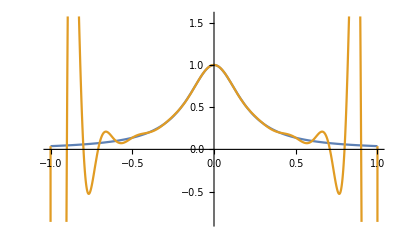

```mathematica
Clear[points,approx,error];
points =Table[{i,f[i]},{i,-1,1,0.1}];
approx[x_] = InterpolatingPolynomial[points,x];
Plot[{f[x],approx[x]},{x,-1,1}]
```

Here we see Runge’s Phenomenon. As we increase the points used in approximating (and thusly the degree of the approximating polynomial), the function oscillates terribly near the ends of the interval. The error here is found the same way as before.

```mathematica
deriv = D[f[x],{x,20}];
Plot[deriv,{x,-1,1}]
FindMaximum[{deriv,-1≤x≤1},{x,0}]
FindMinimum[{deriv,-1≤x≤1},{x,0.03}]
```

-Graphics-

{2.3202×10^32,{x→0.}}

{-1.85257×10^32,{x→0.0287557}}

```mathematica
error = 1/(4(19+1))*2.32019615953125*10^32*((1-(-1))/19)^(19+1)
```

8.09026×10^10

If we sample 100 equidistant points, we find our maximum error of the points sampled is:

```mathematica
max = 0;
inc = 0.02;
For[i=0,i<99,i++,
error =Abs[ f[-1+inc] - approx[-1+inc]];
If[error > max,max = error]
];
Print["The maximum error is " , max]
```

The maximum error is 58.2781

Which is a rather large error! Now, how do we go about decreasing the error? One option is to use what are called Chebyshev nodes. They are nodes that are spread out so that more points lie on the ends of the interval than in the center of the interval. Let’s see how using Chebyshev nodes affects how out approximating polynomial looks when we have 5 points.

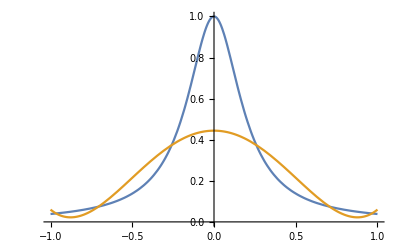

```mathematica
Clear[i,approx];
cNode [i_,n_] = 0.5(-1+1)+0.5(1-(-1))Cos[(2i+1)/(2n+2)Pi];
cPoints = Table[{cNode[i,5],f[cNode[i,5]]},{i,0,5,1}];
approx[x_] = InterpolatingPolynomial[cPoints,x];
Plot[{f[x],approx[x]},{x,-1,1}]
```

Comparing this with the equidistant approximation you can see that while it approximates the ends of the interval fairly accurately, it does not approximate the center as well as the approximation using equidistant points. The maximum error when sampling 100 equidistant points is

```mathematica
max = 0;
inc = 0.02;
For[i=0,i<99,i++,
error =Abs[ f[-1+inc] - approx[-1+inc]];
If[error > max,max = error]
];
Print["The maximum error is " , max]
```

The maximum error is 0.00801269

Our maximum error over the points using equidistant nodes was 0.0895458 so even using only 5 nodes Chebyshev nodes are already more accurate than using equidistant nodes. Now let’s look at using 20 different Chebyshev nodes.

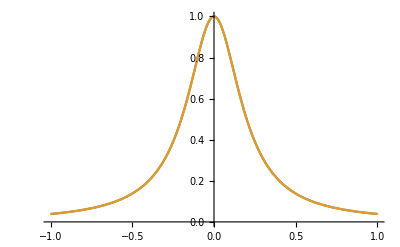

```mathematica
Clear[i,approx, cPoints];
cPoints = Table[{cNode[i,20],f[cNode[i,20]]},{i,0,20,0.1}];
approx[x_] = InterpolatingPolynomial[cPoints,x];
Plot[{f[x],approx[x]},{x,-1,1}]
```

Our maximum error found when we sample 100 equally spaced points is:

```mathematica
max = 0;
inc = 0.02;
For[i=0,i<99,i++,
error =Abs[ f[-1+inc] - approx[-1+inc]];
If[error > max,max = error]
];
Print["The maximum error is " , max]
```

The maximum error is 6.67932×10^-12

This is a much better approximation than when we used equidistant nodes. There appears to be no visual difference between the original function and the approximation. Chebyshev nodes give a much better approximation for functions especially functions like 1/(1+25x^2) which oscillates badly near the end of the interval when using equidistant points. If you want to see Runge’s Phenomenon in action go to https://demonstrations.wolfram.com/RungesPhenomenon/

References
http://practicalcryptography.com/miscellaneous/machine-learning/approximating-function-polynomial/
https://brilliant.org/wiki/chebyshev-polynomials-definition-and-properties/
https://infogalactic.com/info/Chebyshev_nodes
https://en.wikipedia.org/wiki/Runge%27s_phenomenon
https://en.wikipedia.org/wiki/Chebyshev_polynomials
http://www.math.wsu.edu/faculty/genz/448/lessons/l303.pdf